This notebook can be used to replicate the numerical solutions in the main paper. The code in the “function for...” blocks just defines functions. Once that code is in memory, the sensitivity plots in the “(* find ...” blocks can be expanded and used.

## Joint Global/Local Plots

### functions for Global dispersal calculations

```mathematica
Prm6[mA_,mJ_,pA_,pJ_,pB_,s_,r_]:=Module[{p1,p2},(
p1=r(pB pA+(1-pB)pJ);
p2=pB pA/(pB pA+(1-pB)pJ);
(p1^(mA+mJ) Exp[-p1])/((mA+mJ)!)*Binomial[mA+mJ,mA]p2^mA (1-p2)^mJ
)];
```

```mathematica
Prm6invade[mA_?NumericQ,mJ_?NumericQ,pA_?NumericQ,pJ_?NumericQ,p_?NumericQ,s_?NumericQ,r_?NumericQ]:=Module[{p1,p2,Prm},(
p1=N[r(p pA+(1-p)pJ)];
Prm=If[p==0,
(p1^(mJ) Exp[-p1])/((mJ)!)(1-Sign[mA]),
(p1^(mA) Exp[-p1])/((mA)!)(1-Sign[mJ])
];
Prm
)];
```

```mathematica
SolveR2[sAr2_,sJr2_,Ar2_,pr2_,pAr2_,pJr2_,R0r2_]:=Module[{PAx,PA0x,PJ0x},
(
PAx=PA[Ar2,pr2,pAr2,pJr2,R0r2];
PA0x=PA0[Ar2,pr2,pAr2,pJr2,R0r2];
PJ0x=PJ0[Ar2,pr2,pAr2,pJr2,R0r2];
R0r2(PAx sAr2+(1-PAx)sJr2)+(1-R0r2)(PA0x sAr2+PJ0x sJr2)
)];
```

```mathematica
SolveR2Fast[sA_?NumericQ,sJ_?NumericQ,A_?NumericQ,p_?NumericQ,pA_?NumericQ,pJ_?NumericQ,R0_?NumericQ]:=Module[{PrCache,PAx,PA0x,PJ0x,Nmax,nJ,nA},(
Nmax=10;
(* PrCache=Table[Prm6invade[nA,nJ,pA,pJ,p,1,R0],{nA,0,Nmax},{nJ,0,Nmax}]; *)
(* Prob occupied site won by Adult *)
PAx=If[p==0,
NSum[Prm6invade[0,nJ,pA,pJ,p,1,R0](A/(A+nJ)),{nJ,0,Nmax}],
NSum[Prm6invade[nA,0,pA,pJ,p,1,R0]((nA A)/(1+nA A)),{nA,0,Nmax}]
];
(* Prob UNoccupied site won by Adult *)
PA0x=If[p==0,
0,
NSum[Prm6invade[nA,0,pA,pJ,p,1,R0](1),{nA,1,Nmax}]
];
(* Prob UNoccupied site won by Juvenile *)
PJ0x=If[p==0,
NSum[Prm6invade[0,nJ,pA,pJ,p,1,R0](1),{nJ,1,Nmax}],
0
];
R0(PAx sA+(1-PAx)sJ)+(1-R0)(PA0x sA+PJ0x sJ)
)];
```

```mathematica
SolveR3[sA_?NumericQ,sJ_?NumericQ,A_?NumericQ,p_?NumericQ,pA_?NumericQ,pJ_?NumericQ,R0_?NumericQ]:=Module[{Rn,diff,Rn1},(
Rn=R0;
diff=1;
While[diff>0.0001,
Rn1=SolveR2Fast[sA,sJ,A,p,pA,pJ,Rn];
diff=Abs[Rn1-Rn];
Rn=Rn1;
];
Rn
)];
```

```mathematica
SolveR3strict[sA_,sJ_,A_,p_,pA_,pJ_,R0_]:=Module[{Rn,diff,Rn1},(
Rn=R0;
diff=1;
While[diff>0.0001,
Rn1=SolveR2Fast[sA,sJ,A,p,pA,pJ,Rn];
diff=Abs[Rn1-Rn];
Rn=Rn1;
];
Rn
)];
```

```mathematica
SolveR4[sA_?NumericQ,sJ_?NumericQ,A_?NumericQ,p_?NumericQ,pA_?NumericQ,pJ_?NumericQ,R0_?NumericQ]:=Module[{Rn,diff,Rn1},(
Rn=R0;
diff=1;
While[diff>0.0001,
Rn1=SolveR2[sA,sJ,A,p,pA,pJ,Rn];
diff=Abs[Rn1-Rn];
Rn=Rn1;
];
Rn
)];
```

```mathematica
PA[A_,p_,pA_,pJ_,R_]:=(
Nmax=10;
Padult=NSum[Prm6[nA,nJ,pA,pJ,p,1,R](p(nA A)/(1+nA A+nJ)+(1-p)(A(1+nA))/(A+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
Padult
);
```

```mathematica
(* PJ is prob an occupied site is won by a juvenile *)
```

```mathematica
PJ[A_,p_,pA_,pJ_,R_]:=(
Nmax=10;
Pjuv=NSum[Prm6[nA,nJ,pA,pJ,p,1,R](p(1+nJ)/(1+nA A+nJ)+(1-p)nJ/(A+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
Pjuv
);
```

```mathematica
(* PA0 is probability an UNoccupied site is won by an adult *)
```

```mathematica
PA0[A_,p_,pA_,pJ_,R_]:=(
Nmax=10;
Padult=NSum[Prm6[nA,nJ,pA,pJ,p,1,R]((nA A)/(nA A+nJ)),{nA,1,Nmax},{nJ,0,Nmax}];
Padult
);
```

```mathematica
PJ0[A_,p_,pA_,pJ_,R_]:=(
Nmax=10;
Pjuv=NSum[Prm6[nA,nJ,pA,pJ,p,1,R](nJ/(nA A+nJ)),{nA,0,Nmax},{nJ,1,Nmax}];
Pjuv
);
```

```mathematica
Wdiff[A_,p_,rho_,pA_,pJ_,sA_,sJ_]:=Module[{r,Nmax,PBhome,PBaway,WB,PShome,PSaway,WS},(
r=SolveR3[sA,sJ,A,p,pA,pJ,1];
Nmax=10;
PBhome=sJ*NSum[Prm6[nA,nJ,pA,pJ,p,1,r] 1/(1+nA A+nJ),{nA,0,Nmax},{nJ,0,Nmax}];
PBaway=pA*sA*NSum[Prm6[nA,nJ,pA,pJ,p,1,r](p r A/(A+1+nA A+nJ)+(1-p)r A/(A+A+nA A+nJ)+(1-r)A/(A+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
WB=rho PBhome+PBaway;
PShome=sA*NSum[Prm6[nA,nJ,pA,pJ,p,1,r] A/(A+nA A+nJ),{nA,0,Nmax},{nJ,0,Nmax}];
PSaway=pJ*sJ*NSum[Prm6[nA,nJ,pA,pJ,p,1,r](p r 1/(1+1+nA A+nJ)+(1-p)r 1/(1+A+nA A+nJ)+(1-r)1/(1+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
WS=PShome+rho PSaway;
WB-WS
)];
```

```mathematica
WdiffFast[A_?NumericQ,p_?NumericQ,rho_?NumericQ,pA_?NumericQ,pJ_?NumericQ,sA_?NumericQ,sJ_?NumericQ]:=Module[{r,Nmax,PrCache,PBhome,PBaway,WB,PShome,PSaway,WS,nA,nJ},(
r=SolveR3[sA,sJ,A,p,pA,pJ,1];
(*If[r<0.01,Print[{pJ,r}]];*)
Nmax=10;
PrCache=Table[Prm6invade[nA,nJ,pA,pJ,p,1,r],{nA,0,Nmax},{nJ,0,Nmax}];
PBhome=sJ*NSum[PrCache[[nA+1,nJ+1]] 1/(1+nA A+nJ),{nA,0,Nmax},{nJ,0,Nmax}];
PBaway=pA*sA*NSum[PrCache[[nA+1,nJ+1]](p r A/(A+1+nA A+nJ)+(1-p)r A/(A+A+nA A+nJ)+(1-r)A/(A+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
WB=rho PBhome+PBaway;
PShome=sA*NSum[PrCache[[nA+1,nJ+1]] A/(A+nA A+nJ),{nA,0,Nmax},{nJ,0,Nmax}];
PSaway=pJ*sJ*NSum[PrCache[[nA+1,nJ+1]](p r 1/(1+1+nA A+nJ)+(1-p)r 1/(1+A+nA A+nJ)+(1-r)1/(1+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
WS=PShome+rho PSaway;
WB-WS
)];
```

```mathematica
(* function to return p', frequency of B in next season *)
```

```mathematica
Dp[A_,p_,rho_,pA_,pJ_,sA_,sJ_,R_]:=Module[{r,Nmax,PBhome,PBaway,WB,PShome,PSaway,WS,pp},(
r=R;
Nmax=10;
PBhome=sJ*NSum[Prm6[nA,nJ,pA,pJ,p,1,r] 1/(1+nA A+nJ),{nA,0,Nmax},{nJ,0,Nmax}];
PBaway=pA*sA*NSum[Prm6[nA,nJ,pA,pJ,p,1,r](p r A/(A+1+nA A+nJ)+(1-p)r A/(A+A+nA A+nJ)+(1-r)A/(A+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
WB=rho PBhome+PBaway;
PShome=sA*NSum[Prm6[nA,nJ,pA,pJ,p,1,r] A/(A+nA A+nJ),{nA,0,Nmax},{nJ,0,Nmax}];
PSaway=pJ*sJ*NSum[Prm6[nA,nJ,pA,pJ,p,1,r](p r 1/(1+1+nA A+nJ)+(1-p)r 1/(1+A+nA A+nJ)+(1-r)1/(1+nA A+nJ)),{nA,0,Nmax},{nJ,0,Nmax}];
WS=PShome+rho PSaway;
pp=p WB/(p WB+(1-p)WS);
pp-p
)];
```

```mathematica
DR[A_,p_,pA_,pJ_,sA_,sJ_,R_]:=Module[{r},
r=SolveR2[sA,sJ,A,p,pA,pJ,R];
r-R
];
```

### functions for Local dispersal calculations

```mathematica
Prm7[m_,pA_,pJ_,pB_,s_,r_,N_]:=(
p1=r(pB pA+(1-pB)pJ)/2;
Binomial[N,m]p1^m (1-p1)^(N-m)
);
```

```mathematica
SolveR2L[sA_,sJ_,A_,p_,pA_,pJ_,R0_]:=(
PAx=PAL[A,p,pA,pJ,R0];
PA0x=PA0L[A,p,pA,pJ,R0];
PJ0x=PJ0L[A,p,pA,pJ,R0];
R0(PAx sA+(1-PAx)sJ)+(1-R0)(PA0x sA+PJ0x sJ)
);
```

```mathematica
SolveR3L[sA_,sJ_,A_,p_,pA_,pJ_,R0_]:=(
Rn=R0;
diff=1;
While[diff>0.0001,
Rn1=SolveR2L[sA,sJ,A,p,pA,pJ,Rn];
diff=Abs[Rn1-Rn];
Rn=Rn1;
];
Rn
);
```

```mathematica
(* PA is probability that an occupied site is won by an adult *)
```

```mathematica
PAL[A_,p_,pA_,pJ_,R_]:=(
Padult=NSum[Prm7[n,pA,pJ,p,1,R,2](p(n A)/(1+n A)+(1-p)A/(A+n)),{n,0,2}];
Padult
);
```

```mathematica
(* PJ is prob an occupied site is won by a juvenile *)
```

```mathematica
PJL[A_,p_,pA_,pJ_,R_]:=(
Pjuv=NSum[Prm7[n,pA,pJ,p,1,R,2](p 1/(1+n A)+(1-p)n/(A+n)),{n,0,2}];
Pjuv
);
```

```mathematica
(* PA0 is probability an UNoccupied site is won by an adult *)
```

```mathematica
PA0L[A_,p_,pA_,pJ_,R_]:=(
Padult=NSum[Prm7[n,pA,pJ,p,1,R,2](p Sign[n]),{n,1,2}];
Padult
);
```

```mathematica
(* PJ0 is probability an UNoccupied site is won by a juvenile *)
```

```mathematica
PJ0L[A_,p_,pA_,pJ_,R_]:=(
Pjuv=NSum[Prm7[n,pA,pJ,p,1,R,2]((1-p)Sign[n]),{n,1,2}];
Pjuv
);
```

```mathematica
(* compute fitness for general sA,sJ model *)
```

Fitness functions

```mathematica
WdiffL[A_,p_,rho_,pA_,pJ_,sA_,sJ_]:=(
r=SolveR3L[sA,sJ,A,p,pA,pJ,1];
Nmax=2;
PBhome=sJ*NSum[Prm7[n,pA,pJ,p,1,r,2](p 1/(1+n A)+(1-p)1/(1+n)),{n,0,2}];
PBaway=pA*sA*NSum[Prm7[n,pA,pJ,p,1,r,1](p( r A/(A+1+n A)+(1-r)A/(A+n A))+(1-p)(r A/(A+A+n)+(1-r)A/(A+n))),{n,0,1}];
WB=rho PBhome+PBaway;
PShome=sA*NSum[Prm7[n,pA,pJ,p,1,r,2](p A/(A+n A)+(1-p)A/(A+n)),{n,0,2}];
PSaway=pJ*sJ*NSum[Prm7[n,pA,pJ,p,1,r,1](p( r 1/(1+1+n A)+(1-r)1/(1+n A))+(1-p)(r 1/(1+A+n)+(1-r)1/(1+n))),{n,0,1}];
WS=PShome+rho PSaway;
WB-WS
);
```

### Sensitivity Plots

#### (* find rho for given A *)

```mathematica
kpA=0.75;
kpJ=0.75;
ksA=0.75;
ksJ=0.75;
```

```mathematica
Wt[xrho_?NumberQ]:=WdiffFast[2^xA,1,xrho,kpA,kpJ,ksA,ksJ];
tab1=Parallelize[Table[Quiet[FindRoot[Wt[xrho],{xrho,0.5,0,1}]][[1,2]],{xA,0,10,0.1}]];
```

```mathematica
Wt[xrho_?NumberQ]:=WdiffFast[2^xA,0,xrho,kpA,kpJ,ksA,ksJ];
tab2=Parallelize[Table[Quiet[FindRoot[Wt[xrho],{xrho,0.5,0,1}]][[1,2]],{xA,0,10,0.1}]];
```

```mathematica
Wt[xrho_?NumberQ]:=WdiffL[2^xA,1,xrho,kpA,kpJ,ksA,ksJ];
tabL1=Parallelize[Table[Quiet[FindRoot[Wt[xrho],{xrho,0.5,0,1}]][[1,2]],{xA,0,10,0.1}]];
```

```mathematica
Wt[xrho_?NumberQ]:=WdiffL[2^xA,0,xrho,kpA,kpJ,ksA,ksJ];
tabL2=Parallelize[Table[Quiet[FindRoot[Wt[xrho],{xrho,0.5,0,1}]][[1,2]],{xA,0,10,0.1}]];
```

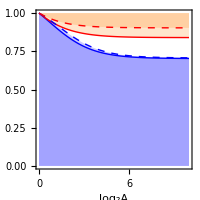

```mathematica
Atick={0,2,6,10};
rtick={0,0.5,1};
fticks={{},{},Atick,rtick};
ListLinePlot[{tab1,tab2,tabL1,tabL2},Frame->True,FrameLabel->{"log_2A","ρ"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},AspectRatio->1,FrameTicks->fticks,ImageSize->200,PlotRange->{{0,10},{0,1}},FrameStyle->(Directive[{FontFamily->"Helvetica",FontSize->12}]),DataRange->{0,10},AxesOrigin->{0,0},Filling->{1->Bottom,2->Top,3->Bottom,4->Top},FillingStyle->{{Orange,Opacity[0.2]},{Blue,Opacity[0.2]}},ImagePadding->{{50,30},{40,20}}]
```

In above, above red curves are where S is not an ESS. Below blue is where B is not an ESS. In between is where both S and B are ESS. Dashed is for local dispersal.

#### (* find dJ for given A *)

```mathematica
kpA=0.9;
ksA=0.8;
ksJ=0.8;
krho=0.5;
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffFast[2^xA,1,krho,kpA,xpJ,ksA,ksJ];
tab1=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.01,1}]][[1,2]],{xA,0,10,0.1}]];
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffFast[2^xA,0,krho,kpA,xpJ,ksA,ksJ];
tab2=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.01,1}]][[1,2]],{xA,0,10,0.1}]];
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffL[2^xA,1,krho,kpA,xpJ,ksA,ksJ];
tabL1=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.01,1}]][[1,2]],{xA,0,10,0.1}]];
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffL[2^xA,0,krho,kpA,xpJ,ksA,ksJ];
tabL2=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.01,1}]][[1,2]],{xA,0,10,0.1}]];
```

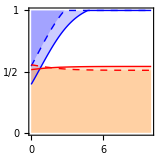

```mathematica
ListLinePlot[{tab1,tab2,tabL1,tabL2},Frame->True,FrameLabel->{"log_2A","dJ"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},AspectRatio->1,FrameTicks->{{0,2,6,10},{0,1/2,1}},ImageSize->160,PlotRange->{{0,10},{0,1}},FrameStyle->(Directive[{FontFamily->"Helvetica",FontSize->12}]),DataRange->{0,10},AxesOrigin->{0,0},Filling->{1->Top,2->Bottom,3->Top,4->Bottom},FillingStyle->{{Blue,Opacity[0.2]},{Orange,Opacity[0.2]}}]
```

#### (* find dJ for dA *)

```mathematica
kA=2^10;
ksA=0.8;
ksJ=0.8;
krho=0.5;
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffFast[kA,1,krho,xpA,xpJ,ksA,ksJ];
tab1=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.49,1}]][[1,2]],{xpA,0.5,1,0.01}]];
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffFast[kA,0,krho,xpA,xpJ,ksA,ksJ];
tab2=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.49,1}]][[1,2]],{xpA,0.5,1,0.01}]];
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffL[kA,1,krho,xpA,xpJ,ksA,ksJ];
tabL1=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.49,1}]][[1,2]],{xpA,0.5,1,0.01}]];
```

```mathematica
Wt[xpJ_?NumberQ]:=WdiffL[kA,0,krho,xpA,xpJ,ksA,ksJ];
tabL2=Parallelize[Table[Quiet[FindRoot[Wt[xpJ],{xpJ,0.75,0.49,1}]][[1,2]],{xpA,0.5,1,0.01}]];
```

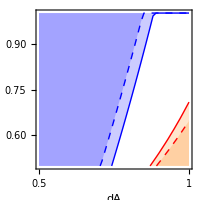

```mathematica
atick={0.5,0.75,1};
fticks={atick,{},{},atick};
ListLinePlot[{tab1,tab2,tabL1,tabL2},Frame->True,FrameLabel->{"dA","dJ"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},AspectRatio->1,ImageSize->200,FrameTicks->fticks,PlotRange->{{0.5,1},{0.5,1}},FrameStyle->(Directive[{FontFamily->"Helvetica",FontSize->12}]),DataRange->{0.5,1},AxesOrigin->{0,0},Filling->{1->Top,2->Bottom,3->Top,4->Bottom},FillingStyle->{{Blue,Opacity[0.2]},{Orange,Opacity[0.2]}},ImagePadding->{{50,30},{40,20}}]
```

#### (* find sJ for sA *) with residency

```mathematica
kA=2^10;
kpA=0.7;
kpJ=0.7;
krho=0.5;
```

```mathematica
Wt[xsJ_?NumberQ]:=WdiffFast[kA,1,krho,kpA,kpJ,xsA,xsJ];
tab1=Parallelize[Table[Quiet[FindRoot[Wt[xsJ],{xsJ,0.75,0.49,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

```mathematica
Wt[xsJ_?NumberQ]:=WdiffFast[kA,0,krho,kpA,kpJ,xsA,xsJ];
tab2=Parallelize[Table[Quiet[FindRoot[Wt[xsJ],{xsJ,0.75,0.49,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

```mathematica
Wt[xsJ_?NumberQ]:=WdiffL[kA,1,krho,kpA,kpJ,xsA,xsJ];
tabL1=Parallelize[Table[Quiet[FindRoot[Wt[xsJ],{xsJ,0.75,0.49,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

```mathematica
Wt[xsJ_?NumberQ]:=WdiffL[kA,0,krho,kpA,kpJ,xsA,xsJ];
tabL2=Parallelize[Table[Quiet[FindRoot[Wt[xsJ],{xsJ,0.75,0.49,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

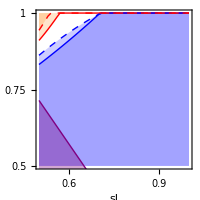

```mathematica
atick={0.5,0.75,1};
fticks={{},atick,atick,{}};
plot1=ListLinePlot[{tab1,tab2,tabL1,tabL2},Frame->True,FrameLabel->{"sJ","sA"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},AspectRatio->1,ImageSize->200,FrameTicks->fticks,PlotRange->{{0.5,1},{0.5,1}},FrameStyle->(Directive[{FontFamily->"Helvetica",FontSize->12}]),DataRange->{0.5,1},AxesOrigin->{0,0},Filling->{1->Bottom,2->Top,3->Bottom,4->Top},FillingStyle->{{Orange,Opacity[0.2]},{Blue,Opacity[0.2]}},ImagePadding->{{50,30},{40,20}}];
plot2=Plot[(1-sA)/kpJ,{sA,0.5,1},PlotStyle->{Purple},Filling->{1->Bottom},FillingStyle->{Directive[Opacity[0.35],Purple]}];
plot3=Plot[1-kpA sA,{sA,0.5,1},PlotStyle->{Red},Filling->{1->Bottom},FillingStyle->{Directive[Opacity[0.35],Red]}];
Show[{plot1,plot2}]
```

#### (* find dA for sA *) with residency

```mathematica
kA=2^1;
kpJ=0.55;
ksJ=0.8;
krho=0.5;
```

```mathematica
kpA=0.77;
ksA=0.65;
```

```mathematica
SolveR3strict[ksA,ksJ,kA,0,kpA,kpJ,0.5]
```

0.177623

```mathematica
SolveR3strict[ksA,ksJ,kA,1,kpA,kpJ,0.5]
```

0.454439

```mathematica
Wt[xpA_?NumberQ]:=WdiffFast[kA,1,krho,xpA,kpJ,xsA,ksJ];
tab1=Parallelize[Table[Quiet[FindRoot[Wt[xpA],{xpA,0.75,0.5,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

```mathematica
Wt[xpA_?NumberQ]:=WdiffFast[kA,0,krho,xpA,kpJ,xsA,ksJ];
tab2=Parallelize[Table[Quiet[FindRoot[Wt[xpA],{xpA,0.75,0.5,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

```mathematica
Wt[xpA_?NumberQ]:=WdiffL[kA,1,krho,xpA,kpJ,xsA,ksJ];
tabL1=Parallelize[Table[Quiet[FindRoot[Wt[xpA],{xpA,0.75,0.5,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

```mathematica
Wt[xpA_?NumberQ]:=WdiffL[kA,0,krho,xpA,kpJ,xsA,ksJ];
tabL2=Parallelize[Table[Quiet[FindRoot[Wt[xpA],{xpA,0.75,0.5,1}]][[1,2]],{xsA,0.5,1,0.01}]];
```

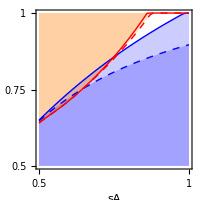

```mathematica
ListLinePlot[{tab1,tab2,tabL1,tabL2},Frame->True,FrameLabel->{"sA","pA"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},AspectRatio->1,ImageSize->200,FrameTicks->{{0.5,0.75,1},{0.5,0.75,1}},PlotRange->{{0.5,1},{0.5,1}},FrameStyle->(Directive[{FontFamily->"Helvetica",FontSize->12}]),DataRange->{0.5,1},AxesOrigin->{0,0},Filling->{1->Bottom,2->Top,3->Bottom,4->Top},FillingStyle->{{Orange,Opacity[0.2]},{Blue,Opacity[0.2]}},ImagePadding->{{50,30},{40,20}}]
```

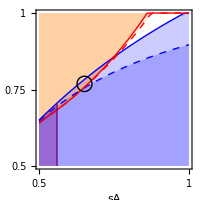

```mathematica
plot1=ListLinePlot[{tab1,tab2,tabL1,tabL2},Frame->True,FrameLabel->{"sA","pA"},PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},AspectRatio->1,ImageSize->200,FrameTicks->{{0.5,0.75,1},{0.5,0.75,1}},PlotRange->{{0.5,1},{0.5,1}},FrameStyle->(Directive[{FontFamily->"Helvetica",FontSize->12}]),DataRange->{0.5,1},AxesOrigin->{0,0},Filling->{1->Bottom,2->Top,3->Bottom,4->Top},FillingStyle->{{Orange,Opacity[0.2]},{Blue,Opacity[0.2]}},ImagePadding->{{50,30},{40,20}}];
line1=Graphics[{Purple,Line[{{0.56,0.5},{0.56,0.705}}]}];
shade1=Graphics[{Purple,Opacity[0.35],Polygon[{{0.56,0.5},{0.56,0.705},{0.5,0.65},{0.5,0.5}}]}];
pt1=Graphics[Circle[{0.65,0.77},0.025]];
Show[{plot1,pt1,line1,shade1}]
```

### Vector Field plot with isoclines (Global dispersal only)

```mathematica
kA=2^1;
krho=0.5;
kdA=0.77;
kdJ=0.55;
ksA=0.65;
ksJ=0.8;
```

```mathematica
tab3=Parallelize[Table[{Dp[kA,p,krho,kdA,kdJ,ksA,ksJ,R],DR[kA,p,kdA,kdJ,ksA,ksJ,R]},{p,0.01,0.99,0.05},{R,0.01,0.99,0.05}]];
```

```mathematica
fopt[R_?NumberQ]:=Dp[kA,p,krho,kdA,kdJ,ksA,ksJ,R];
tabisop=Table[Quiet[FindRoot[fopt[R],{R,0.5,0.01,0.99}]][[1,2]],{p,0.01,0.99,0.05}];
```

```mathematica
fopt[R_?NumberQ]:=DR[kA,p,kdA,kdJ,ksA,ksJ,R];
tabisoR=Table[Quiet[FindRoot[fopt[R],{R,0.5,0.01,0.99}]][[1,2]],{p,0.01,0.99,0.05}];
```

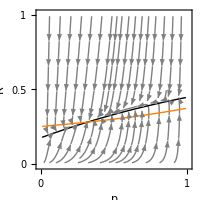

```mathematica
plot1=ListStreamPlot[tab3,FrameLabel->{p,R},DataRange->{{0.01,0.99},{0.01,0.99}},StreamStyle->Directive[{Gray,Thin}],StreamPoints->33,StreamScale->Large,ImageSize->200,ImagePadding->{{50,30},{40,20}},FrameTicks->{{0,0.5,1},{0,0.5,1},{},{}},FrameStyle->(Directive[{FontFamily->"Helvetica",FontSize->12}])];
isoR=ListLinePlot[tabisoR,DataRange->{0.01,0.99},PlotStyle->Black];
isop=ListLinePlot[tabisop,DataRange->{0.01,0.99},PlotStyle->Orange];
Show[plot1,isoR,isop]
```

```mathematica
(* EQ around p==0.3, R==0.28 *)
```

### Simple simulation from analytical expectations

```mathematica
tmax=2000;
Rt=1;
pt=0.9;
Rlist=ConstantArray[0,tmax];
plist=ConstantArray[0,tmax];
For[t=1,t<tmax+1,t++,
Rtt=Rt+DR[kA,pt,kdA,kdJ,ksA,ksJ,Rt];
ptt=pt+Dp[kA,pt,krho,kdA,kdJ,ksA,ksJ,Rt];
Rlist[[t]]=Rtt;
plist[[t]]=ptt;
Rt=Rtt;
pt=ptt;
];
```

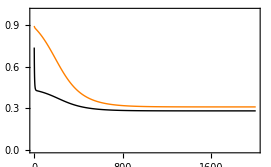

```mathematica
ListLinePlot[{plist,Rlist},PlotRange->{All,{0,1}},PlotStyle->{Orange,Black},Frame->True]
```